```mathematica
PacletInstall[CloudObject["https://wolfr.am/DevWQCF"], ForceVersionInstall -> True];
<< Wolfram`QuantumFramework`;
```

QuantumPartialTrace::shdw: Symbol QuantumPartialTrace appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumState::shdw: Symbol QuantumState appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

```mathematica
QuantumState[{1/Sqrt[2],1/Sqrt[2]},2]["Formula"]
QuantumState[{1/Sqrt[2],I/Sqrt[2]},2]["Formula"]
```

0/(√2)+1/(√2)

0/(√2)+(ⅈ 1)/(√2)

This is the Lattice Simulation Code

```mathematica
addMatrix[n_]:=SparseArray[Table[{If[i+1>n,i-(n-1),i+1],i}->1,{i,n}]];
subMatrix[n_]:=SparseArray[Table[{If[i==1,n,i-1],i}->1,{i,n}]];

addOp= QuantumOperator[addMatrix[#1],{},#1] &;
subOp= QuantumOperator[subMatrix[#1],{},#1] &;

(*ctrAddn = QuantumOperator[{"Controlled", addOp[qudit], list{ctrlclosed}, list{ctrlopen} }, list{targets}];*)
ctrlAdd = QuantumOperator[{"Controlled",addOp[#1], #2, #3}, #4] &;
ctrlSub = QuantumOperator[{"Controlled",subOp[#1], #2, #3}, #4] &;

oracle[gate_,N_]:=ctrlSub[N,{3},{4},{2}]@ctrlAdd[N,{4},{3},{2}]@ctrlSub[N,{3,4},{},{1}]@ctrlAdd[N,{},{3,4},{1}]@QuantumOperator[gate,{3}]@QuantumOperator[gate,{4}];

simulation[T_,coinState1_,coinState2_,gateType_]:=Module[{N,qubitState,systemState,systemOracle},
N=2T + 1;
qubitState=QuantumState[SparseArray[{T+1}->1,{N}],N]; (*This needs to act on the first and second qubits*)
systemState=QuantumTensorProduct[qubitState,qubitState,coinState1,coinState2];
systemOracle=oracle[gateType,N];
NestList[systemOracle,systemState,T]
]
```

Let's run some simulations!

```mathematica
P=20;
G=2P +1;

jIndex = Join @@ {#}[[ConstantArray[1, #2]]] &;
jIndex=jIndex[Range[-P,P], G];
iIndex = Flatten@Transpose[{#}[[ConstantArray[1, #2]]]] &;
iIndex=iIndex[Range[-P,P], G];

collabels =  Range[-P,P]; 
rowlabels = Range[-P,P];
rowticks = Thread[{ Range[G], rowlabels}];
colticks = Thread[{ Range[G], collabels}];

output1=simulation[P,QuantumState["0"],QuantumState["0"],"H"][[-1]];
preResult1=Diagonal[QuantumPartialTrace[output1, {3,4}]["DensityMatrix"]];
result1=ArrayReshape[preResult1,{G,G}];
listResult1=Normal[preResult1];
exportData1=Table[{iIndex[[i]],jIndex[[i]],N[listResult1[[i]]]},{i,G^2}];
Export["Lattice_P20_H_00.csv",exportData1];
CopyFile["Lattice_P20_H_00.csv",CloudObject["Lattice_P20_H_00.csv"],OverwriteTarget->True]

output2=simulation[P,QuantumState[{1/Sqrt[2],I/Sqrt[2]},2],QuantumState[{1/Sqrt[2],I/Sqrt[2]},2],"H"][[-1]];
preResult2=Diagonal[QuantumPartialTrace[output2, {3,4}]["DensityMatrix"]];
result2=ArrayReshape[preResult2,{G,G}];
listResult2=Normal[preResult2];
exportData2=Table[{iIndex[[i]],jIndex[[i]],N[listResult2[[i]]]},{i,G^2}];
Export["Lattice_P20_H_++.csv",exportData2];
CopyFile["Lattice_P20_H_++.csv",CloudObject["Lattice_P20_H_++.csv"],OverwriteTarget->True]

output3=simulation[P,QuantumState[{1/Sqrt[2],-1/Sqrt[2]},2],QuantumState[{1/Sqrt[2],-1/Sqrt[2]},2],"H"][[-1]];
preResult3=Diagonal[QuantumPartialTrace[output3, {3,4}]["DensityMatrix"]];
result3=ArrayReshape[preResult3,{G,G}];
listResult3=Normal[preResult3];
exportData3=Table[{iIndex[[i]],jIndex[[i]],N[listResult3[[i]]]},{i,G^2}];
Export["Lattice_P20_H_00-01-10+11.csv",exportData3];
CopyFile["Lattice_P20_H_00-01-10+11.csv",CloudObject["Lattice_P20_H_00-01-10+11.csv"],OverwriteTarget->True]

output4=simulation[P,QuantumState["0"],QuantumState[{1/Sqrt[2],1/Sqrt[2]},2],"H"][[-1]];
preResult4=Diagonal[QuantumPartialTrace[output4, {3,4}]["DensityMatrix"]];
result4=ArrayReshape[preResult4,{G,G}];
listResult4=Normal[preResult4];
exportData4=Table[{iIndex[[i]],jIndex[[i]],N[listResult4[[i]]]},{i,G^2}];
Export["Lattice_P20_H_00+01.csv",exportData4];
CopyFile["Lattice_P20_H_00+01.csv",CloudObject["Lattice_P20_H_00+01.csv"],OverwriteTarget->True]



(*graph=Rasterize[MatrixPlot[result1, ColorFunction -> "BlueGreenYellow",FrameTicks -> {rowticks, colticks},PlotLegends -> Automatic], "Image"];*)
```

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Lattice_P20_H_00.csv]

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Lattice_P20_H_++.csv]

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Lattice_P20_H_00-01-10+11.csv]

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Lattice_P20_H_00+01.csv]

```mathematica
P=20;
G=2P +1;

jIndex = Join @@ {#}[[ConstantArray[1, #2]]] &;
jIndex=jIndex[Range[-P,P], G];
iIndex = Flatten@Transpose[{#}[[ConstantArray[1, #2]]]] &;
iIndex=iIndex[Range[-P,P], G];
output5=simulation[P,QuantumState[{1/Sqrt[2],I/Sqrt[2]},2],QuantumState[{1/Sqrt[2],1/Sqrt[2]},2],"H"][[-1]];
preResult5=Diagonal[QuantumPartialTrace[output5, {3,4}]["DensityMatrix"]];
result5=ArrayReshape[preResult5,{G,G}];
listResult5=Normal[preResult5];
exportData5=Table[{iIndex[[i]],jIndex[[i]],N[listResult5[[i]]]},{i,G^2}];
Export["Lattice_P20_H_00+01+i10+i11.csv",exportData5];
CopyFile["Lattice_P20_H_00+01+i10+i11.csv",CloudObject["Lattice_P20_H_00+01+i10+i11.csv"],OverwriteTarget->True]

output6=simulation[P,QuantumState["0"],QuantumState[{1/Sqrt[2],I/Sqrt[2]},2],"H"][[-1]];
preResult6=Diagonal[QuantumPartialTrace[output6, {3,4}]["DensityMatrix"]];
result6=ArrayReshape[preResult6,{G,G}];
listResult6=Normal[preResult6];
exportData6=Table[{iIndex[[i]],jIndex[[i]],N[listResult6[[i]]]},{i,G^2}];
Export["Lattice_P20_H_00+i01.csv",exportData6];
CopyFile["Lattice_P20_H_00+i01.csv",CloudObject["Lattice_P20_H_00+i01.csv"],OverwriteTarget->True]
```

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Lattice_P20_H_00+01+i10+i11.csv]

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Lattice_P20_H_00+i01.csv]

We can now make a simple extension to the 1d line.

```mathematica
addMatrix[n_]:=SparseArray[Table[{If[i+1>n,i-(n-1),i+1],i}->1,{i,n}]];
subMatrix[n_]:=SparseArray[Table[{If[i==1,n,i-1],i}->1,{i,n}]];

addOp= QuantumOperator[addMatrix[#1],{},#1] &;
subOp= QuantumOperator[subMatrix[#1],{},#1] &;

(*ctrAddn = QuantumOperator[{"Controlled", addOp[qudit], list{ctrlclosed}, list{ctrlopen} }, list{targets}];*)
ctrlAdd = QuantumOperator[{"Controlled",addOp[#1], #2, #3}, #4] &;
ctrlSub = QuantumOperator[{"Controlled",subOp[#1], #2, #3}, #4] &;

lineOracle[gate_,N_]:=ctrlSub[N,{2},{},{1}]@ctrlAdd[N,{},{2},{1}]@QuantumOperator[gate,{2}];

lineSim[T_,coinState_,gateType_]:=Module[{N,qubitState,systemState,systemOracle},
N=2T + 1;
qubitState=QuantumState[SparseArray[{T+1}->1,{N}],N];
systemState=QuantumTensorProduct[qubitState,coinState];
systemOracle=lineOracle[gateType,N];
NestList[systemOracle,systemState,T]
]
```

Run a basic example

```mathematica
L=20;
lineValues=Range[-L,L];

lineOutput1=lineSim[L,QuantumState["0"],"H"][[-1]];
lineResult1= Normal[Diagonal[QuantumPartialTrace[lineOutput1, {2}]["DensityMatrix"]]];
lineExportData1=Table[{lineValues[[i]],N[lineResult1[[i]]]},{i,2L + 1}];

lineOutput2=lineSim[L,QuantumState["1"],"H"][[-1]];
lineResult2= Normal[Diagonal[QuantumPartialTrace[lineOutput2, {2}]["DensityMatrix"]]];
lineExportData2=Table[{lineValues[[i]],N[lineResult2[[i]]]},{i,2L + 1}];

lineOutput3=lineSim[L,QuantumState[{1/Sqrt[2],I/Sqrt[2]},2],"H"][[-1]];
lineResult3= Normal[Diagonal[QuantumPartialTrace[lineOutput3, {2}]["DensityMatrix"]]];
lineExportData3=Table[{lineValues[[i]],N[lineResult3[[i]]]},{i,2L + 1}];

Export["Line_L20_H_0.csv",lineExportData1];
CopyFile["Line_L20_H_0.csv",CloudObject["Line_L20_H_0.csv"],OverwriteTarget->True]
Export["Line_L20_H_1.csv",lineExportData2];
CopyFile["Line_L20_H_1.csv",CloudObject["Line_L20_H_1.csv"],OverwriteTarget->True]
Export["Line_L20_H_+.csv",lineExportData3];
CopyFile["Line_L20_H_+.csv",CloudObject["Line_L20_H_Right.csv"],OverwriteTarget->True]
```

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Line_L20_H_0.csv]

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Line_L20_H_1.csv]

CloudObject[https://www.wolframcloud.com/obj/gabrielwaite1999/Line_L20_H_Right.csv]

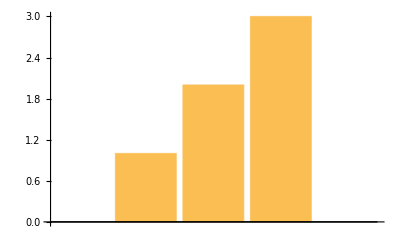

```mathematica
BarChart[{1, 2, 3}, ChartLabels -> Automatic]
```

```mathematica
Module[{yy},
  f[x_, y_: 0, z_: yy] := Block[{yy = y}, {x, y, z}]
]
```

{1,2}

{1,x}